```mathematica
SetDirectory[NotebookDirectory[]];
```

## 4 loop running coupling

```mathematica
(* form hep-ph 9703284, vermaseren, larin, Ritbergen *)
ΛQCD=0.2145; 
(* so that for nF=5 we get alpha_s(mz=91.188)=0.1185 (PDG value) 
note that pdg also quotes λqcd=0.214 for nf=5 everything seems consistent*)

(*QCD*)
Nc=3.;CA=Nc; nF=3;
CF=(Nc^2-1)/(2 Nc);
(*coeft of the renormalization group equations*)
β0[Nf_]=(-11Nc+2Nf)/12;
β1[Nf_]=(-68 Nc^2+20Nc Nf+12CF Nf)/(3 32);
β2[Nf_]=-((2857-(5033/9)Nf+(325/27) Nf^2)/128); (*for Nc=3 only*)
β3[Nf_]=((-1)/256)((149753/6+3564 Zeta[3])-(1078361/162+(6508/27) Zeta[3])Nf+(50065/162+(6472/81)Zeta[3])Nf^2+(1093/729) Nf^3);(*for Nc=3 only*)

γ0[Nf_]=3/4 CF;
γ1[Nf_]=(1/16)(202/3-(20/9)Nf);(*for Nc=3 only*)
γ2[Nf_]=(1/64)(1249+(-(2216/27)-(160/3) Zeta[3])Nf-(140/81) Nf^2);(*for Nc=3 only*)
γ3[Nf_]=(1/256)(4603055/162+(135680/27) Zeta[3]-8800Zeta[5]+(-(91723/27)-(34192/9) Zeta[3]+880 Zeta[4]+(18400/9)Zeta[5])Nf+(5242/243+(800/9) Zeta[3]-(160/3)Zeta[4])Nf^2+(-(332/243)+(64/27) Zeta[3])Nf^3);

b0[Nf_]=-((8β0[Nf])/(2(4π)^2));
b1[Nf_]=-((32 β1[Nf])/(2(4π)^2));

(* Initial conditions of the RG equations, μ in units of Λ_MSbar *)

(*gf[μ_]=1/√(2 b0 Log[μ]+b1 Log[2 Log[μ]]/b0);*)
gf[t_]=1/(√(b0[Nf] t+b1[Nf] Log[t]/b0[Nf]));
asf[t_,Nf_]=(-1)/(β0[Nf] t)-(β1[Nf] Log[t])/(β0[Nf]^3 t^2)-( β1[Nf]^2(Log[t]^2-Log[t]-1)+β2[Nf] β0[Nf])/(β0[Nf]^5 t^3)+(1/(β0[Nf]^7 t^4))( β1[Nf]^3(-Log[t]^3+5/2 Log[t]^2+2Log[t]-1/2)-3 β1[Nf] β2[Nf] β0[Nf] Log[t]+1/2 β3[Nf] β0[Nf]^2);
μ0=2;
t0=Log[μ0^2];
tf=10000 t0;
(*solution of the RG equation to 3 loop*)
mcharm=1.275;(*m(m) in msbar*)
mbottom=4.18;
nf[t_]=If[t<Log[mcharm^2/ΛQCD^2],3,If[t<Log[mbottom^2/ΛQCD^2],4,5]];
sg4=Quiet[NDSolve[{D[as[t],t]==+β0[nf[t]] as[t]^2+β1[nf[t]] as[t]^3+ β2[nf[t]] as[t]^4+ β3[nf[t]] as[t]^5,as[tf]==asf[tf,nf[tf]]},as,{t,t0,tf},AccuracyGoal->14,WorkingPrecision->32,MaxSteps->10000000]];

a4t[t_]= Part[Evaluate[as[t]/.sg4],1];
g4[μ_]=2 π √Part[Evaluate[as[Log[μ^2/ΛQCD^2]]/.sg4],1];
```

## Functions

```mathematica
R=20000;
Mc=1.4691897661033038;
Mb=4.882;
kfinal={0.6856700331366409,-0.31661256911352553};(*100k run*)
kfinalu={0.9065399936425322,-0.36858869824209667};
kfinall={0.4648000726307495,-0.2646364399849544};
αcont={0.5129548374487685,0.002435119807500435};(*10k run*)
σcont={0.16999653850906107,0.000838106749908169};
ccont={-0.1611740456186636,0.002474788649682089};
conv=0.197327;
ReVsbVac=8/10;
```

```mathematica
ReV[r_,mD_,α_,σ_,c_]:=c-α mD-α Exp[-mD r]/r+(2 σ)/mD-(ⅇ^(-mD r) (2+mD r) σ)/mD;
```

```mathematica
ImVc[r_,mD_,α_,T_]:=T α Quiet[2NIntegrate[z/((z^2+1)^2)(1-Sinc[mD r z]),{z,0,∞},MaxRecursion->20]];
ImVs[r_,mD_,σ_,T_]:=1/4 mD √π r^3 T σ MeijerG[{{-1/2,-1/2},{}},{{1/2,1/2},{-3/2,-1}},(mD^2 r^2)/4];
```

### Self energies

```mathematica
mDcalmu[T_,μ_,c_,d_]:=SetPrecision[Re[Sqrt[Nc/3+nF/6+nF/(2 π^2)(μ/3)^2/T^2]g4[2π √(T^2+μ^2/π^2)]T+1/(4π)Nc g4[2π √(T^2+μ^2/π^2)]^2 T Log[Sqrt[Nc/3+nF/6]/g4[2π √(T^2+μ^2/π^2)]]+c g4[2π √(T^2+μ^2/π^2)]^2 T+d g4[2π √(T^2+μ^2/π^2)]^3 T ],30];
```

```mathematica
Πpar[θ_,mD_,u_]:=SetPrecision[mD^2/2((2-2 u^2-u^4 Cos[θ]^2 Sin[θ]^2)/((1-u^2 Sin[θ]^2)^2)-((2+u^2 Sin[θ]^2)(1-u^2)u Cos[θ])/(2(1-u^2 Sin[θ]^2)^(5/2))Log[(u Cos[θ]+√(1-u^2 Sin[θ]^2))/(u Cos[θ]-√(1-u^2 Sin[θ]^2))]),30];
```

### IIT paper

#### Potentials

```mathematica
ReVcpp[r_,mD_,u_,α_,c_]:=Re[c-α/r+α  NIntegrate[Sin[θ] √Πpar[θ,mD,u] Exp[-√Πpar[θ,mD,u]r Cos[θ]],{θ,0,π/2},MaxRecursion->20,WorkingPrecision->20]];(*INCORRECT*)
ReVspp[r_,mD_,u_,σ_]:=Re[σ NIntegrate[Sin[θ] 1/(√Πpar[θ,mD,u])Exp[-√Πpar[θ,mD,u]r Cos[θ]],{θ,0,π/2},MaxRecursion->20,WorkingPrecision->20]];(*INCORRECT*)
ReVsp[r_,mD_,u_,σ_]:=σ NIntegrate[Sin[θ] 1/Re[√Πpar[θ,mD,u]] Exp[-Re[√Πpar[θ,mD,u]]r Cos[θ]],{θ,0,π/2},MaxRecursion->20,WorkingPrecision->20];(*OUR MODEL DIFFERS HERE*)
ReVcp[r_,mD_,u_,α_,c_]:=c-α mD-α/r+α NIntegrate[Sin[θ]Re[√Πpar[θ,mD,u]]Exp[-Re[√Πpar[θ,mD,u]]r Cos[θ]],{θ,0,π/2},MaxRecursion->20,WorkingPrecision->20];(*WE USE THIS ONE*)
```

```mathematica
ImVcp[r_,mD_,u_,α_,T_]:=2 α T Quiet[NIntegrate[Sin[x]((2+u^2 Sin[x]^2)(1-u^2)^(3/2))/(2(1-u^2 Sin[x]^2)^(5/2))mD^2/(Πpar[x,mD,u]-Conjugate[Πpar[x,mD,u]])(Sinh[√Πpar[x,mD,u] r Cos[x]]SinhIntegral[√Πpar[x,mD,u] r Cos[x]]-Cosh[√Πpar[x,mD,u] r Cos[x]]CoshIntegral[√Πpar[x,mD,u] r Cos[x]]-Sinh[√Conjugate[Πpar[x,mD,u]] r Cos[x]]SinhIntegral[√Conjugate[Πpar[x,mD,u]] r Cos[x]]+Cosh[√Conjugate[Πpar[x,mD,u]] r Cos[x]]CoshIntegral[√Conjugate[Πpar[x,mD,u]] r Cos[x]]),{x,0,π/2},MaxRecursion->20,WorkingPrecision->20]];(*WE USE THIS ONE*)
```

#### Permittivities

```mathematica
ϵRepp[r_,mD_,u_]:=Re[1/(4π)(2/r NIntegrate[Cos[θ]Sin[θ]Πpar[θ,mD,u]Exp[-√Πpar[θ,mD,u]r Cos[θ]],{θ,0,π/2}]-NIntegrate[Cos[θ]^2 Sin[θ] Πpar[θ,mD,u]^(3/2)Exp[-√Πpar[θ,mD,u]r Cos[θ]],{θ,0,π/2}])];(*INCORRECT*)
ϵRep[r_,mD_,u_]:=1/(4π)(2/r NIntegrate[Cos[θ]Sin[θ]Re[Πpar[θ,mD,u]]Exp[-Re[√Πpar[θ,mD,u]]r Cos[θ]],{θ,0,π/2}]-NIntegrate[Cos[θ]^2 Sin[θ]Re[Πpar[θ,mD,u]^(3/2)]Exp[-Re[√Πpar[θ,mD,u]]r Cos[θ]],{θ,0,π/2}]);(*OLD*)
```

```mathematica
ϵImp[r_,mD_,u_,T_]:=
1/(2π)Re[T NIntegrate[Sin[x]((2+u^2 Sin[x]^2)(1-u^2)^(3/2))/(2(1-u^2 Sin[x]^2)^(5/2))mD^2/(Πpar[x,mD,u]-Conjugate[Πpar[x,mD,u]])1/r Cos[x] (2 √Conjugate[Πpar[x,mD,u]] (CoshIntegral[r √Conjugate[Πpar[x,mD,u]] Cos[x]] Sinh[r √Conjugate[Πpar[x,mD,u]] Cos[x]]-Cosh[r √Conjugate[Πpar[x,mD,u]] Cos[x]] SinhIntegral[r √Conjugate[Πpar[x,mD,u]] Cos[x]])+r Conjugate[Πpar[x,mD,u]] Cos[x] (Cosh[r √Conjugate[Πpar[x,mD,u]] Cos[x]] CoshIntegral[r √Conjugate[Πpar[x,mD,u]] Cos[x]]-Sinh[r √Conjugate[Πpar[x,mD,u]] Cos[x]] SinhIntegral[r √Conjugate[Πpar[x,mD,u]] Cos[x]])+√Πpar[x,mD,u] (-CoshIntegral[r Cos[x] √Πpar[x,mD,u]] (r Cos[x] Cosh[r Cos[x] √Πpar[x,mD,u]] √Πpar[x,mD,u]+2 Sinh[r Cos[x] √Πpar[x,mD,u]])+(2 Cosh[r Cos[x] √Πpar[x,mD,u]]+r Cos[x] √Πpar[x,mD,u] Sinh[r Cos[x] √Πpar[x,mD,u]]) SinhIntegral[r Cos[x] √Πpar[x,mD,u]])),{x,0,π/2},WorkingPrecision->20]];(*UNREGULATED*)
```

```mathematica
D[Sin[θ]f[θ,mD,u]Exp[-f[θ,mD,u]r Cos[θ]],{r,2}]+2/r D[Sin[θ]f[θ,mD,u]Exp[-f[θ,mD,u]r Cos[θ]],r]//FullSimplify
```

(ⅇ^(-r Cos[θ] f[θ,mD,u]) Cos[θ] f[θ,mD,u]^2 (-2+r Cos[θ] f[θ,mD,u]) Sin[θ])/r

```mathematica
ϵRep1[r_,mD_,u_]:=Quiet[NIntegrate[(ⅇ^(-r Cos[θ] Re[√Πpar[θ,mD,u]]) Cos[θ] Re[√Πpar[θ,mD,u]]^2 (-2+r Cos[θ] Re[√Πpar[θ,mD,u]]) Sin[θ])/r,{θ,0,π/2},MaxRecursion->20,WorkingPrecision->20]];(*WE USE THIS ONE*)
```

```mathematica
Integrate[(ⅇ^(-r Cos[θ] mD) Cos[θ] mD^2 (-2+r Cos[θ] mD) Sin[θ])/(4π r),{θ,0,π/2}]
```

-(ⅇ^(-mD r) mD^2)/(4 π r)

### Tabs

```mathematica
ReVsTab[mD1_,u1_,σ1_]:=Block[{u=u1,mD=mD1,σ=σ1,inter0,inter1,tab,inter2,inter3,tab1,tab0},tab0=ParallelTable[{r,σ r^2 ϵRep1[r,mD,u]},{r,10^-10,500,1/100}];
inter0=Interpolation[tab0];
inter1[r_]:=Quiet[NIntegrate[inter0[r1],{r1,0,r}]];
tab=ParallelTable[{r,inter1[r]+σ},{r,0,100,1/20}];
inter2=Interpolation[tab];
inter3[r_]:=Quiet[NIntegrate[inter2[r1],{r1,0,r}]];
tab1=ParallelTable[{r,inter3[r]},{r,0,100,1/20}];
Export["vel_pot/ReVsu"<>ToString[Round[100 u]]<>"u.dat",tab1];];
```

```mathematica
reg=303689/100000;
```

```mathematica
ImVsTab[mD1_,u1_,σ1_,T1_]:=Block[{u=u1,mD=mD1,σ=σ1,T=T1,tab0,tab1,inter0,inter1,inter2,temp,tab2},tab0=Table[{r,4π σ r^2 ϵImp[r,mD,u,T]},{r,10^-10,100,1/10}];
inter0=Interpolation[tab0];
inter1[r_]:=Quiet[NIntegrate[inter0[r1],{r1,10^-10,r}]];
temp=inter1[10^-10];
tab1=ParallelTable[{r,inter1[r]-temp},{r,10^-10,100,1/10}];
inter1=Interpolation[tab1];
inter2[r_]:=Quiet[NIntegrate[inter1[r1],{r1,10^-10,r}]];
tab2=ParallelTable[{r,inter2[r]},{r,10^-10,100,1/10}];
Export["vel_pot/ImVsu"<>ToString[Round[100 u]]<>"u.dat",tab2];];
```

### Make potentials

```mathematica
uscan=Join[Table[i,{i,1/10,9/10,1/10}],{99/100}]
```

{1/10,1/5,3/10,2/5,1/2,3/5,7/10,4/5,9/10,99/100}

```mathematica
Do[ReVsTab[mDcalmu[0.155,0,kfinalu[[1]],kfinalu[[2]]],uscan[[i]],σcont[[1]]];,{i,1,Length[uscan]}]
```

```mathematica
Do[Quiet[ImVsTab[SetPrecision[mDcalmu[0.155,0,kfinalu[[1]],kfinalu[[2]]],30],uscan[[i]],SetPrecision[σcont[[1]],30],155/1000]];,{i,1,Length[uscan]}]
```

```mathematica
ImVcuTab[n_]:=Block[{temp,temp1},temp=ImVcp[10^-10,SetPrecision[mDcalmu[0.155,0,kfinalu[[1]],kfinalu[[2]]],30],uscan[[n]],SetPrecision[αcont[[1]],30],155/1000];temp1=ParallelTable[{r,ImVcp[r,SetPrecision[mDcalmu[0.155,0,kfinalu[[1]],kfinalu[[2]]],30],uscan[[n]],SetPrecision[αcont[[1]],30],155/1000]-temp},{r,1/1000,60,1/100}];
Export["vel_pot/ImVcu"<>ToString[Round[100 uscan[[n]]]]<>"u.dat",temp1];]
```

```mathematica
Do[ImVcuTab[i],{i,1,Length[uscan]}]
```

```mathematica
ImVsuTab[n_]:=Block[{temp},temp=Join[ParallelTable[{r,ReVcp[r,mDcalmu[0.155,0,kfinalu[[1]],kfinalu[[2]]],uscan[[n]],αcont[[1]],ccont[[1]]]},{r,1/1000,100,1/100}],{{500,ReVcp[500,mDcalmu[0.155,0,kfinalu[[1]],kfinalu[[2]]],uscan[[n]],αcont[[1]],ccont[[1]]]}}];Export["vel_pot/ReVcu"<>ToString[Round[100 uscan[[n]]]]<>"u.dat",temp];]
```

```mathematica
Do[ImVsuTab[i],{i,1,Length[uscan]}]
```

## Plot potentials

```mathematica
uscan=Join[Table[i,{i,1/10,9/10,1/10}],{99/100}]
```

{1/10,1/5,3/10,2/5,1/2,3/5,7/10,4/5,9/10,99/100}

```mathematica
Block[{data},Do[data=ToExpression[Import["vel_pot/ReVsu"<>ToString[Round[100uscan[[n]]]]<>".dat"]];data=Append[data,{20000,data[[-1,2]]}];ReVsu[n]=Interpolation[data,InterpolationOrder->1],{n,Length[uscan]}]];
```

```mathematica
Block[{data},Do[data=ToExpression[Import["vel_pot/ReVcu"<>ToString[Round[100uscan[[n]]]]<>".dat"]];data=Append[data,{20000,data[[-1,2]]}];ReVcu[n]=Interpolation[data,InterpolationOrder->1],{n,Length[uscan]}]];
```

```mathematica
Block[{data},Do[data=ToExpression[Import["vel_pot/ImVcu"<>ToString[Round[100uscan[[n]]]]<>".dat"]];data=Append[data,{20000,data[[-1,2]]}];ImVcu[n]=Interpolation[data,InterpolationOrder->1],{n,Length[uscan]}]];
```

```mathematica
Block[{data},Do[data=ToExpression[Import["vel_pot/ImVsu"<>ToString[Round[100uscan[[n]]]]<>".dat"]];data=Append[data,{20000,data[[-1,2]]}];ImVsu[n]=Interpolation[data,InterpolationOrder->1],{n,Length[uscan]}]];
```

```mathematica
Block[{data},data=ToExpression[Import["vel_pot/ImVsu"<>ToString[Round[100 uscan[[8]]]]<>"T250l.dat"]][[;;535]];
data=Append[data,{20000,data[[-1,2]]}];
ImVsu[8]=Interpolation[data,InterpolationOrder->1]];
```

```mathematica
uSetS={"v=0","v=0.5","v=0.9","v=0.99"};
```

```mathematica
mD1=mDcalmu[155/1000,0,kfinal[[1]],kfinal[[2]]]
```

0.207411256204937832769985561754

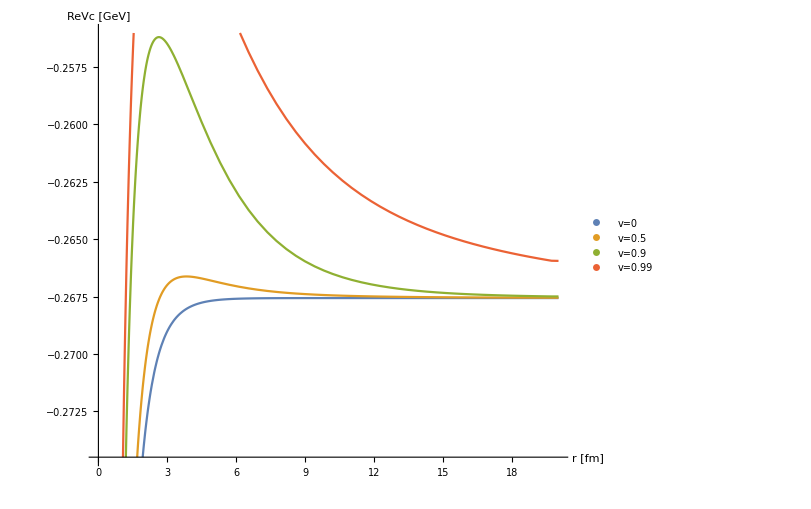

```mathematica
Plot[{ReV[r/0.197,mD1,αcont[[1]],0,ccont[[1]]],ReVcu[5][r/0.197],ReVcu[9][r/0.197],ReVcu[10][r/0.197]},{r,0,20},AxesStyle->Directive[FontSize->25,Thickness->0.002,FontFamily->"CMU Serif",Black],BaseStyle->{FontSize->14},AspectRatio->0.85,AxesLabel->{"r [fm]","ReVc [GeV]"},ImageSize->{600,600},PlotLegends->Placed[PointLegend[uSetS, LegendMarkerSize->25,LegendLayout->{"Row",3},LabelStyle->{FontFamily->"CMU Serif"}],{0.7,0.7}],BaseStyle->{FontSize->14}]
```

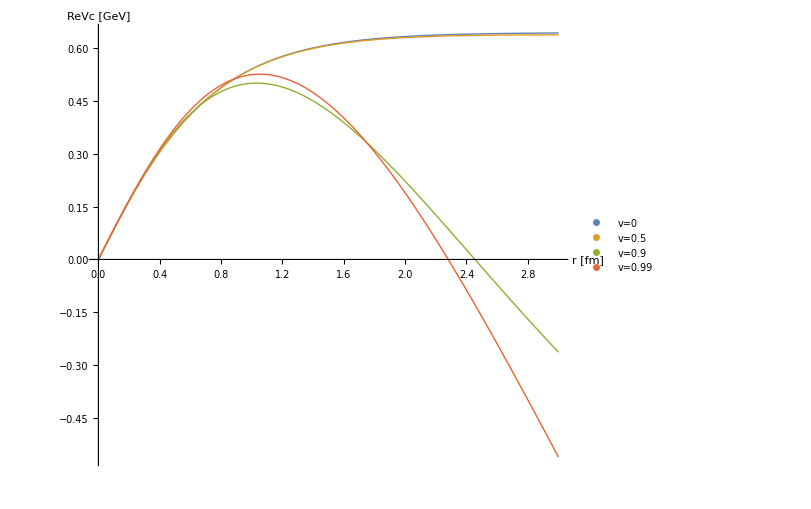

```mathematica
Plot[{ReV[r/0.197,mD1,0,σcont[[1]],0],ReVsu[1][r/0.197],ReVsu[9][r/0.197],ReVsu[10][r/0.197]},{r,0,3},AxesStyle->Directive[FontSize->25,Thickness->0.002,FontFamily->"CMU Serif",Black],BaseStyle->{FontSize->18},AspectRatio->0.85,AxesLabel->{"r [fm]","ReVc [GeV]"},ImageSize->{600,600},PlotStyle->Thick,PlotLegends->Placed[PointLegend[uSetS, LegendMarkerSize->25,LegendLayout->{"Row",3},LabelStyle->{FontFamily->"CMU Serif"}],{0.4,0.2}]]
```

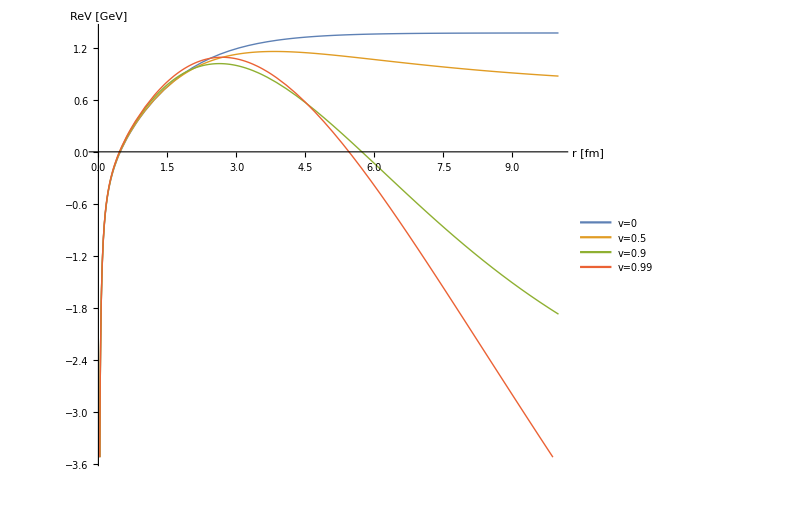

```mathematica
Plot[{ReV[r/0.197,mD1,αcont[[1]],σcont[[1]],ccont[[1]]],ReVsu[5][r/0.197]+ReVcu[5][r/0.197],ReVsu[9][r/0.197]+ReVcu[9][r/0.197],ReVsu[10][r/0.197]+ReVcu[10][r/0.197]},{r,0,10},AxesStyle->Directive[FontSize->30,Thickness->0.002,FontFamily->"CMU Serif",Black],BaseStyle->{FontSize->20},AspectRatio->0.85,AxesLabel->{"r [fm]","ReV [GeV]"},ImageSize->{600,600},PlotStyle->Thick,PlotLegends->Placed[LineLegend[uSetS, LegendMarkerSize->25,LegendLayout->{"Row",3},LabelStyle->{FontFamily->"CMU Serif"}],{0.4,0.3}]]
```

```mathematica
Export["ReVu0_par.dat",Table[{N[r],ReV[r/0.197,mD1,αcont[[1]],σcont[[1]],ccont[[1]]]},{r,1/100,10,1/10}]]
```

ReVu0_par.dat

```mathematica
Export["ReVu5_par.dat",Table[{N[r],ReVsu[5][r/0.197]+ReVcu[5][r/0.197]},{r,1/100,10,1/10}]]
```

ReVu5_par.dat

```mathematica
Export["ReVu9_par.dat",Table[{N[r],ReVsu[9][r/0.197]+ReVcu[9][r/0.197]},{r,1/100,10,1/10}]]
```

ReVu9_par.dat

```mathematica
Export["ReVu99_par.dat",Table[{N[r],ReVsu[10][r/0.197]+ReVcu[10][r/0.197]},{r,1/100,10,1/10}]]
```

ReVu99_par.dat

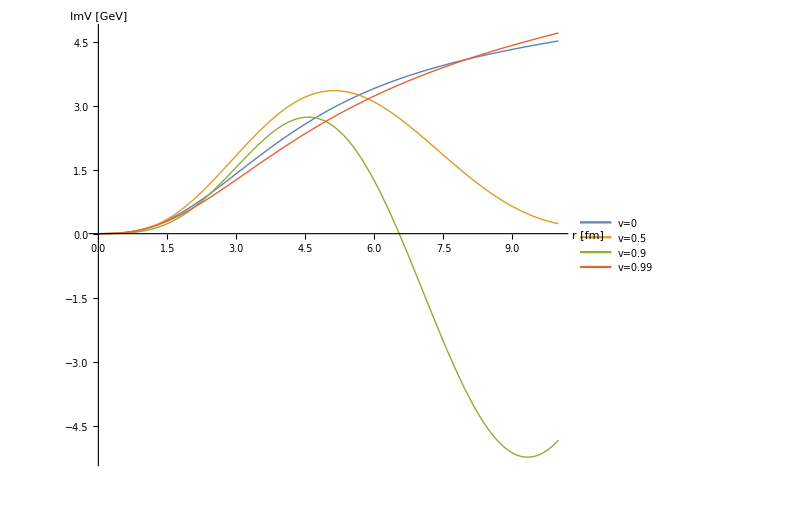

```mathematica
Plot[{Re[ImVcu[5][r/0.197]]+ImVsu[5][r/0.197],Re[ImVcu[9][r/0.197]]+ImVsu[9][r/0.197],Re[ImVcu[10][r/0.197]]+ImVsu[10][r/0.197],ImVc[r/0.197,mD1,αcont[[1]],0.155]+ImVs[r/0.197,mD1,σcont[[1]],0.155]},{r,1/1000,10},AxesStyle->Directive[FontSize->30,Thickness->0.002,FontFamily->"CMU Serif",Black],BaseStyle->{FontSize->20},AspectRatio->0.85,AxesLabel->{"r [fm]","ImV [GeV]"},ImageSize->{600,600},PlotStyle->Thick,PlotLegends->Placed[LineLegend[uSetS, LegendMarkerSize->25,LegendLayout->{"Row",3},LabelStyle->{FontFamily->"CMU Serif"}],{0.35,0.2}]]
```

```mathematica
Export["ImVu0_par.dat",Table[{N[r],ImVc[r/0.197,mD1,αcont[[1]],0.155]+ImVs[r/0.197,mD1,σcont[[1]],0.155]},{r,1/100,10,1/10}]]
```

ImVu0_par.dat

```mathematica
Export["ImVu5_par.dat",Table[{N[r],Re[ImVsu[5][r/0.197]+ImVcu[5][r/0.197]]},{r,1/100,10,1/10}]]
```

ImVu5_par.dat

```mathematica
Export["ImVu9_par.dat",Table[{N[r],Re[ImVsu[9][r/0.197]+ImVcu[9][r/0.197]]},{r,1/100,10,1/10}]]
```

ImVu9_par.dat

```mathematica
Export["ImVu99_par.dat",Table[{N[r],Re[ImVsu[10][r/0.197]+ImVcu[10][r/0.197]]},{r,1/100,10,1/10}]]
```

ImVu99_par.dat

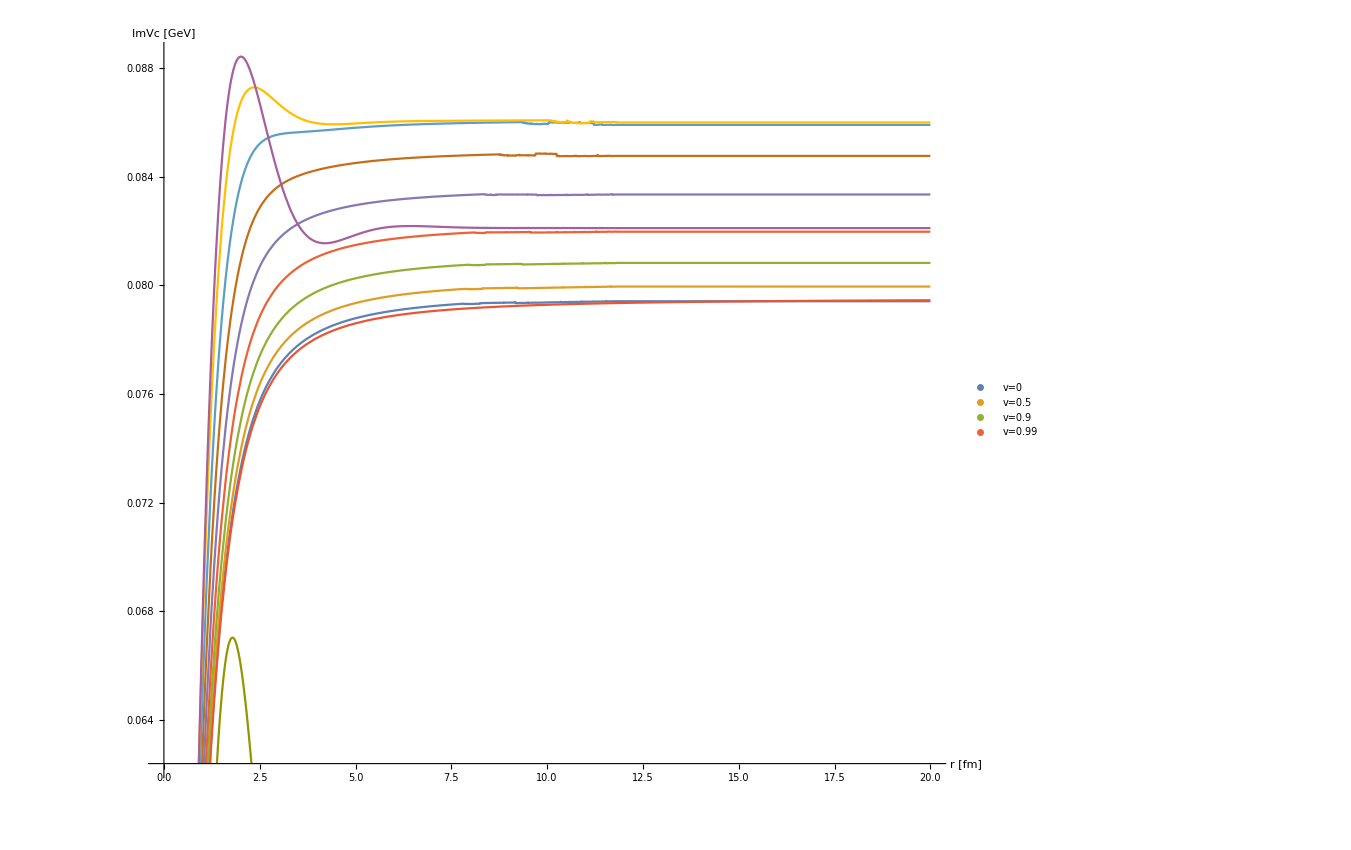

```mathematica
Plot[{Re[ImVcu[1][r/0.197]],Re[ImVcu[2][r/0.197]],Re[ImVcu[3][r/0.197]],Re[ImVcu[4][r/0.197]],Re[ImVcu[5][r/0.197]],Re[ImVcu[6][r/0.197]],Re[ImVcu[7][r/0.197]],Re[ImVcu[8][r/0.197]],Re[ImVcu[9][r/0.197]],Re[ImVcu[10][r/0.197]],ImVc[r/0.197,mD1,αcont[[1]],0.155]},{r,1/1000,20},AxesStyle->Directive[FontSize->25,Thickness->0.004,FontFamily->"Helvetica",Black],BaseStyle->{FontSize->14},AspectRatio->0.85,AxesLabel->{"r [fm]","ImVc [GeV]"},ImageSize->{1000,1000},PlotLegends->Placed[PointLegend[uSetS, LegendMarkerSize->25,LegendLayout->{"Row",3}],{0.8,0.3}],BaseStyle->{FontSize->14}]
```

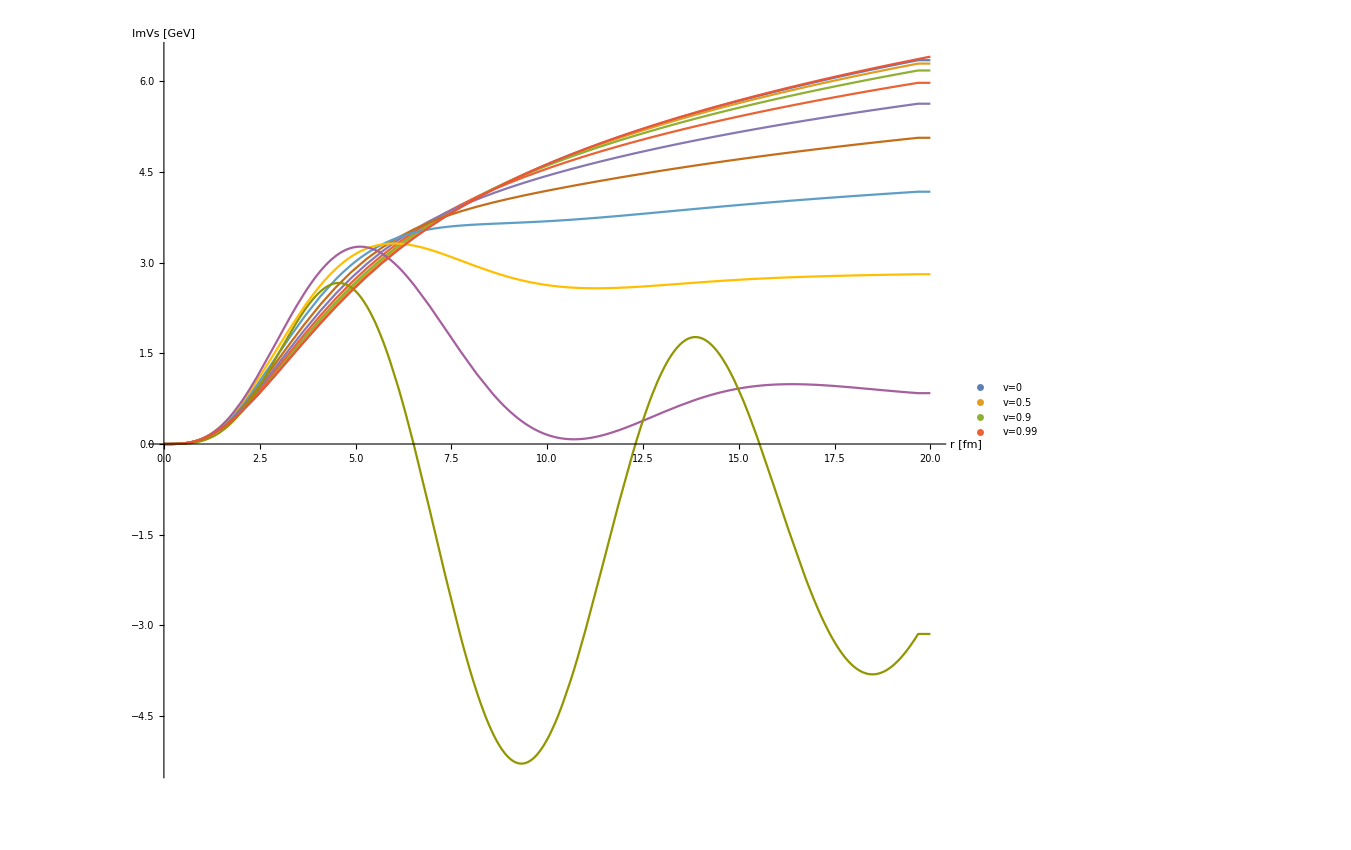

```mathematica
Plot[{Re[ImVsu[1][r/0.197]],Re[ImVsu[2][r/0.197]],Re[ImVsu[3][r/0.197]],Re[ImVsu[4][r/0.197]],Re[ImVsu[5][r/0.197]],Re[ImVsu[6][r/0.197]],Re[ImVsu[7][r/0.197]],Re[ImVsu[8][r/0.197]],Re[ImVsu[9][r/0.197]],Re[ImVsu[10][r/0.197]],ImVs[r/0.197,mD1,σcont[[1]],0.155]},{r,1/1000,20},AxesStyle->Directive[FontSize->25,Thickness->0.004,FontFamily->"Helvetica",Black],BaseStyle->{FontSize->14},AspectRatio->0.85,AxesLabel->{"r [fm]","ImVs [GeV]"},ImageSize->{1000,1000},PlotLegends->Placed[PointLegend[uSetS, LegendMarkerSize->25,LegendLayout->{"Row",3}],{0.8,0.3}],BaseStyle->{FontSize->14}]
```

## Spectra

### Modules

```mathematica
ParallelSow[expr_]:=Sow[expr];
SetSharedFunction[ParallelSow];
```

```mathematica
δ=1/100; 
dω=0.0002;
```

#### Charmonium s-wave

```mathematica
swaveccspectra[u_]:=Block[{α=αcont[[1]],c=ccont[[1]],M=Mc,l=0,ωmin=-1,ωmax=2,ccss,inf,ρtable,ω,rhow,gr0,s1,V},
V[r_]:=ReVsu[u][r]+ReVcu[u][r]+ⅈ(ImVsu[u][r]+ImVcu[u][r]);
ρtable=ParallelDo[ω=ωmin+(it-1) dω M;inf=40+500*it*dω;
(*s0=NDSolve[{(ω-(l(l+1))/(M r^2)-Re[V[r]]+ⅈ Abs[Im[V[r]]])gr[r]+1/M gr''[r]==0, 
gr'[δ]==2 δ(α M)^2-3/4 δ^2(M α)^3,
 gr[δ]== δ^2(α M)^2-1/4 δ^3(M α)^3},gr,{r,δ,inf},PrecisionGoal->10,MaxSteps->1000000];
gr1[r_]=(gr[r]/.s0)_⟦1⟧;*)
s01=NDSolve[{(ω-(l(l+1))/(M r^2)-Re[V[r]]+ⅈ Abs[Im[V[r]]])gr[r]+1/M gr''[r]==0, 
gr'[δ]==(α M)-δ(M α)^2,
 gr[δ]==δ(α M)- 1/2 δ^2(α M)^2},gr,{r,δ,inf}];
gr0[r_]=(gr[r]/.s01)_⟦1⟧;
s1=NDSolve[{rho'[x]==-(6 Nc M^2 α)/(4π)Im[1/(gr0[x])^2(*+36/(gr1[x])^2*)],rho[δ]==0},rho,{x,δ,inf}];
rhow[r_]=(rho[r]/.s1)_⟦1⟧;
ParallelSow[{ω+2M,rhow[inf]}],{it,1,(ωmax-ωmin)/(dω M)}]//Reap//Last//First;

ccss=ParallelTable[{ρtable[[i,1]],(-ρtable[[i,2]])/ρtable[[i,1]]^2},{i,1,Length[ρtable]}];
Export["cc/swccu"<>ToString[Round[10u]]<>"spectrau.dat",Sort[ccss]];
];
```

```mathematica
swavebbspectra[u_]:=Block[{α=αcont[[1]],c=ccont[[1]],M=Mb,l=0,ωmin=-1,ωmax=3,ccss,inf,ρtable,ω,rhow,gr0,s1,V},
V[r_]:=ReVsu[u][r]+ReVcu[u][r]+ⅈ(ImVsu[u][r]+ImVcu[u][r]);
ρtable=ParallelDo[ω=ωmin+(it-1) dω M;inf=40+500*it*dω;
(*s0=NDSolve[{(ω-(l(l+1))/(M r^2)-Re[V[r]]+ⅈ Abs[Im[V[r]]])gr[r]+1/M gr''[r]==0, 
gr'[δ]==2 δ(α M)^2-3/4 δ^2(M α)^3,
 gr[δ]== δ^2(α M)^2-1/4 δ^3(M α)^3},gr,{r,δ,inf},PrecisionGoal->10,MaxSteps->1000000];
gr1[r_]=(gr[r]/.s0)_⟦1⟧;*)
s01=NDSolve[{(ω-(l(l+1))/(M r^2)-Re[V[r]]+ⅈ Abs[Im[V[r]]])gr[r]+1/M gr''[r]==0, 
gr'[δ]==(α M)-δ(M α)^2,
 gr[δ]==δ(α M)- 1/2 δ^2(α M)^2},gr,{r,δ,inf}];
gr0[r_]=(gr[r]/.s01)_⟦1⟧;
s1=NDSolve[{rho'[x]==-(6 Nc M^2 α)/(4π)Im[1/(gr0[x])^2(*+36/(gr1[x])^2*)],rho[δ]==0},rho,{x,δ,inf}];
rhow[r_]=(rho[r]/.s1)_⟦1⟧;
ParallelSow[{ω+2M,rhow[inf]}],{it,1,(ωmax-ωmin)/(dω M)}]//Reap//Last//First;

ccss=ParallelTable[{ρtable[[i,1]],(-ρtable[[i,2]])/ρtable[[i,1]]^2},{i,1,Length[ρtable]}];
Export["bb/swbbu"<>ToString[Round[10u]]<>"spectrau.dat",Sort[ccss]];
];
```

```mathematica
Do[swaveccspectra[i],{i,5,10}]
```

```mathematica
Do[swavebbspectra[i],{i,1,10}]
```

```mathematica
tab10=Import["bb/swccu100spectra.dat"];
tab20=Import["bb/swccu200spectra.dat"];
tab30=Import["bb/swccu300spectra.dat"];
tab40=Import["bb/swccu400spectra.dat"];
tab50=Import["bb/swccu500spectra.dat"];
tab60=Import["bb/swccu600spectra.dat"];
tab70=Import["bb/swccu700spectra.dat"];
tab80=Import["bb/swccu800spectra.dat"];
```

```mathematica
tab90=Import["bb/swccu900spectra.dat"];
```

```mathematica
tab1=Import["bb/swccu1000spectra.dat"];
```

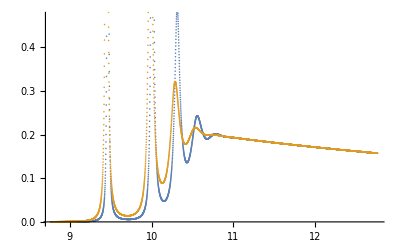

```mathematica
ListPlot[{tab1,tab10}]
```

```mathematica
ctab10=Import["cc/swccu100spectra.dat"];
ctab20=Import["cc/swccu200spectra.dat"];
ctab30=Import["cc/swccu300spectra.dat"];
ctab40=Import["cc/swccu400spectra.dat"];
ctab50=Import["cc/swccu500spectra.dat"];
ctab60=Import["cc/swccu600spectra.dat"];
ctab70=Import["cc/swccu700spectra.dat"];
ctab80=Import["cc/swccu800spectra.dat"];
ctab90=Import["cc/swccu900spectra.dat"];
ctab1=Import["cc/swccu1000spectra.dat"];
```

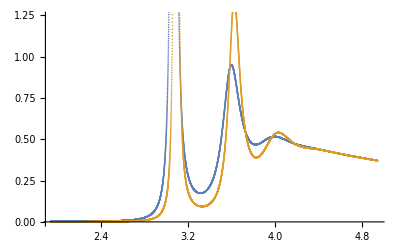

```mathematica
ListPlot[{ctab10,ctab1}]
```